## Step 1. Mode Expansions

nb. In the Phase Field Crystal dimensionless units, the magnitude of the principal RLVs should be unity (with respect to square phase’s).

### Triangular (hexagonal) lattice

The lattice vectors:

```mathematica
Subscript[a, 1]={(-2a)/(√3),0,0};
Subscript[a, 2]={-a/(√3),a,0};
Subscript[a, 3]={0,0,a};
```

The reciprocal lattice vectors:

```mathematica
vol = Dot[Subscript[a, 1],Cross[Subscript[a, 2],Subscript[a, 3]]];
Subscript[b, 1]=2π Cross[Subscript[a, 2],Subscript[a, 3]]/vol;
Subscript[b, 2]=2π Cross[Subscript[a, 3],Subscript[a, 1]]/vol;

Subscript[b, 1]=Drop[Subscript[b, 1],-1]
Subscript[b, 2]=Drop[Subscript[b, 2],-1]
```

{-(√3 π)/a,-π/a}

{0,(2 π)/a}

The 1st mode (1,0), (0,1), (-1,-1) :

```mathematica
r={x,y};
ExpToTrig[ Exp[I*(Dot[Subscript[b, 1],r])]+Exp[-I*(Dot[Subscript[b, 1],r])]+ Exp[I*(Dot[Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 2],r])]+ Exp[I*(Dot[-Subscript[b, 1]-Subscript[b, 2],r])]+Exp[-I*(Dot[-Subscript[b, 1]-Subscript[b, 2],r])]]
```

2 Cos[(2 π y)/a]+2 Cos[(√3 π x)/a-(π y)/a]+2 Cos[(√3 π x)/a+(π y)/a]

The 2nd mode (-1, -2), (-2, -1), (-1, 1) :

```mathematica
r={x,y};
ExpToTrig[ Exp[I*(Dot[-Subscript[b, 1]-2*Subscript[b, 2],r])]+Exp[-I*(Dot[-Subscript[b, 1]-2*Subscript[b, 2],r])]+ Exp[I*(Dot[-2*Subscript[b, 1]-Subscript[b, 2],r])]+Exp[-I*(Dot[-2*Subscript[b, 1]-Subscript[b, 2],r])]+ Exp[I*(Dot[-Subscript[b, 1]+Subscript[b, 2],r])]+Exp[-I*(Dot[-Subscript[b, 1]+Subscript[b, 2],r])]]
```

2 Cos[(2 √3 π x)/a]+2 Cos[(√3 π x)/a-(3 π y)/a]+2 Cos[(√3 π x)/a+(3 π y)/a]

The mode expansion (for triangular phase, 1-mode expansion is adopted so B=0):

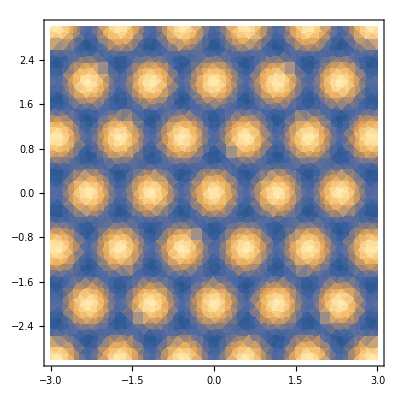

```mathematica
Subscript[n, t][n_,a_,A_,B_,x_,y_]:=n+A( Cos[(2 π y)/a]+ Cos[(√3 π x)/a-(π y)/a]+Cos[(√3 π x)/a+(π y)/a])+B(Cos[(2 √3 π x)/a]+Cos[(√3 π x)/a-(3 π y)/a]+ Cos[(√3 π x)/a+(3 π y)/a])
DensityPlot[Subscript[n, t][0,1,1,0,x,y], {x,-3,3},{y,-3,3}]
```

The period along x is (2a)/(√3), along y is 2a.

### Square lattice

The lattice vectors:

```mathematica
Subscript[a, 1]={a,0,0};
Subscript[a, 2]={0,a,0};
Subscript[a, 3]={0,0,a};
```

The reciprocal lattice vectors:

```mathematica
vol = Dot[Subscript[a, 1],Cross[Subscript[a, 2],Subscript[a, 3]]];
Subscript[b, 1]=2π Cross[Subscript[a, 2],Subscript[a, 3]]/vol;
Subscript[b, 2]=2π Cross[Subscript[a, 3],Subscript[a, 1]]/vol;

Subscript[b, 1]=Drop[Subscript[b, 1],-1]
Subscript[b, 2]=Drop[Subscript[b, 2],-1]
```

{(2 π)/a,0}

{0,(2 π)/a}

The 1st mode (1,0), (0,1),:

```mathematica
r={x,y};
ExpToTrig[ Exp[I*(Dot[Subscript[b, 1],r])]+Exp[-I*(Dot[Subscript[b, 1],r])]+ Exp[I*(Dot[Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 2],r])]]
```

2 Cos[(2 π x)/a]+2 Cos[(2 π y)/a]

The 2nd mode (1, 1), (1, -1) :

```mathematica
r={x,y};
ExpToTrig[ Exp[I*(Dot[Subscript[b, 1]+Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 1]+Subscript[b, 2],r])]+ Exp[I*(Dot[Subscript[b, 1]-Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 1]-Subscript[b, 2],r])]]
```

2 Cos[(2 π x)/a-(2 π y)/a]+2 Cos[(2 π x)/a+(2 π y)/a]

The mode expansion (for square phase, 2-mode expansion is adopted so B neq 0):

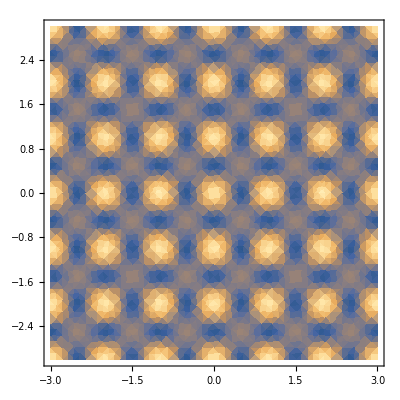

```mathematica
Subscript[n, s][n_,a_,A_,B_,x_,y_]:=n+A(  Cos[(2 π x)/a]+Cos[(2 π y)/a])+B( Cos[(2 π x)/a-(2 π y)/a]+ Cos[(2 π x)/a+(2 π y)/a])
DensityPlot[Subscript[n, s][0,1,1,1,x,y], {x,-3,3},{y,-3,3}]
```

The period along x is a, along y is a.

### BCC lattice

The lattice vectors:

```mathematica
Subscript[a, 1]={(√2 a)/2,(√2 a)/2,-(√2 a)/2};
Subscript[a, 2]={-(√2 a)/2,(√2 a)/2,(√2 a)/2};
Subscript[a, 3]={(√2 a)/2,-(√2 a)/2,(√2 a)/2};
```

The reciprocal lattice vectors:

```mathematica
vol = Dot[Subscript[a, 1],Cross[Subscript[a, 2],Subscript[a, 3]]];
Subscript[b, 1]=2π Cross[Subscript[a, 2],Subscript[a, 3]]/vol
Subscript[b, 2]=2π Cross[Subscript[a, 3],Subscript[a, 1]]/vol
Subscript[b, 3]=2π Cross[Subscript[a, 1],Subscript[a, 2]]/vol
```

{(√2 π)/a,(√2 π)/a,0}

{0,(√2 π)/a,(√2 π)/a}

{(√2 π)/a,0,(√2 π)/a}

The 1st mode (1,0,0), (0,1,0), (0,0,1), (1,-1,0), (0,1,-1), (-1,0,1) :

```mathematica
r={x,y,z};
ExpToTrig[ Exp[I*(Dot[Subscript[b, 1],r])]+Exp[-I*(Dot[Subscript[b, 1],r])]+ Exp[I*(Dot[Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 2],r])]+Exp[I*(Dot[Subscript[b, 3],r])]+Exp[-I*(Dot[Subscript[b, 3],r])]+Exp[I*(Dot[Subscript[b, 1]-Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 1]-Subscript[b, 2],r])]+Exp[I*(Dot[Subscript[b, 2]-Subscript[b, 3],r])]+Exp[-I*(Dot[Subscript[b, 2]-Subscript[b, 3],r])]+Exp[I*(Dot[-Subscript[b, 1]+Subscript[b, 3],r])]+Exp[-I*(Dot[-Subscript[b, 1]+Subscript[b, 3],r])]]
```

2 Cos[(√2 π x)/a-(√2 π y)/a]+2 Cos[(√2 π x)/a+(√2 π y)/a]+2 Cos[(√2 π x)/a-(√2 π z)/a]+2 Cos[(√2 π y)/a-(√2 π z)/a]+2 Cos[(√2 π x)/a+(√2 π z)/a]+2 Cos[(√2 π y)/a+(√2 π z)/a]

The 2nd mode (1, 1,-1), (1, -1,1), (-1, 1,1) :

```mathematica
r={x,y,z};
ExpToTrig[ Exp[I*(Dot[Subscript[b, 1]+Subscript[b, 2]-Subscript[b, 3],r])]+Exp[-I*(Dot[Subscript[b, 1]+Subscript[b, 2]-Subscript[b, 3],r])]+ Exp[I*(Dot[Subscript[b, 1]-Subscript[b, 2]+Subscript[b, 3],r])]+Exp[-I*(Dot[Subscript[b, 1]-Subscript[b, 2]+Subscript[b, 3],r])]+ Exp[I*(Dot[-Subscript[b, 1]+Subscript[b, 2]+Subscript[b, 3],r])]+Exp[-I*(Dot[-Subscript[b, 1]+Subscript[b, 2]+Subscript[b, 3],r])]]
```

2 Cos[(2 √2 π x)/a]+2 Cos[(2 √2 π y)/a]+2 Cos[(2 √2 π z)/a]

The mode expansion (for bcc phase, 1-mode expansion is adopted so B=0):

```mathematica
Subscript[n, b][n_,a_,A_,B_,x_,y_,z_]:=n+A( Cos[(√2 π x)/a-(√2 π y)/a]+ Cos[(√2 π x)/a+(√2 π y)/a]+Cos[(√2 π x)/a-(√2 π z)/a]+ Cos[(√2 π y)/a-(√2 π z)/a]+ Cos[(√2 π x)/a+(√2 π z)/a]+Cos[(√2 π y)/a+(√2 π z)/a])+B(Cos[(2 √3 π x)/a-(2 π y)/(√3 a)-(2 π z)/(√3 a)]+Cos[(2 π x)/(√3 a)-(2 √3 π y)/a+(2 π z)/(√3 a)]+Cos[(2 π x)/(√3 a)+(2 π y)/(√3 a)-(2 √3 π z)/a])
DensityPlot3D[Subscript[n, b][0,1,1,0,x,y,z], {x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

The period along x is √2 a, along y is √2 a,along z is √2 a.

### FCC lattice

The lattice vectors:

```mathematica
Subscript[a, 1]={(√3 a)/2,(√3 a)/2,0};
Subscript[a, 2]={0,(√3 a)/2,(√3 a)/2};
Subscript[a, 3]={(√3 a)/2,0,(√3 a)/2};
```

The reciprocal lattice vectors:

```mathematica
vol = Dot[Subscript[a, 1],Cross[Subscript[a, 2],Subscript[a, 3]]];
Subscript[b, 1]=2π Cross[Subscript[a, 2],Subscript[a, 3]]/vol
Subscript[b, 2]=2π Cross[Subscript[a, 3],Subscript[a, 1]]/vol
Subscript[b, 3]=2π Cross[Subscript[a, 1],Subscript[a, 2]]/vol
```

{(2 π)/(√3 a),(2 π)/(√3 a),-(2 π)/(√3 a)}

{-(2 π)/(√3 a),(2 π)/(√3 a),(2 π)/(√3 a)}

{(2 π)/(√3 a),-(2 π)/(√3 a),(2 π)/(√3 a)}

The 1st mode (1,0,0), (0,1,0), (0,0,1), (-1,-1,-1):

```mathematica
r={x,y,z};
ExpToTrig[ Exp[I*(Dot[Subscript[b, 1],r])]+Exp[-I*(Dot[Subscript[b, 1],r])]+ Exp[I*(Dot[Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 2],r])]+Exp[I*(Dot[Subscript[b, 3],r])]+Exp[-I*(Dot[Subscript[b, 3],r])]+Exp[I*(Dot[-Subscript[b, 1]-Subscript[b, 2]-Subscript[b, 3],r])]+Exp[-I*(Dot[-Subscript[b, 1]-Subscript[b, 2]-Subscript[b, 3],r])]]
```

2 Cos[(2 π x)/(√3 a)-(2 π y)/(√3 a)-(2 π z)/(√3 a)]+2 Cos[(2 π x)/(√3 a)+(2 π y)/(√3 a)-(2 π z)/(√3 a)]+2 Cos[(2 π x)/(√3 a)-(2 π y)/(√3 a)+(2 π z)/(√3 a)]+2 Cos[(2 π x)/(√3 a)+(2 π y)/(√3 a)+(2 π z)/(√3 a)]

The 2nd mode (1, 1,0), (1, 0,1), (0, 1,1) :

```mathematica
r={x,y,z};
ExpToTrig[ Exp[I*(Dot[Subscript[b, 1]+Subscript[b, 2],r])]+Exp[-I*(Dot[Subscript[b, 1]+Subscript[b, 2],r])]+ Exp[I*(Dot[Subscript[b, 1]+Subscript[b, 3],r])]+Exp[-I*(Dot[Subscript[b, 1]+Subscript[b, 3],r])]+ Exp[I*(Dot[Subscript[b, 2]+Subscript[b, 3],r])]+Exp[-I*(Dot[Subscript[b, 2]+Subscript[b, 3],r])]]
```

2 Cos[(4 π x)/(√3 a)]+2 Cos[(4 π y)/(√3 a)]+2 Cos[(4 π z)/(√3 a)]

The mode expansion (for fcc phase, 2-mode expansion is adopted so B neq 0):

```mathematica
Subscript[n, f][n_,a_,A_,B_,x_,y_,z_]:=n+A( Cos[(2 π x)/(√3 a)-(2 π y)/(√3 a)-(2 π z)/(√3 a)]+ Cos[(2 π x)/(√3 a)+(2 π y)/(√3 a)-(2 π z)/(√3 a)]+Cos[(2 π x)/(√3 a)-(2 π y)/(√3 a)+(2 π z)/(√3 a)]+ Cos[(2 π x)/(√3 a)+(2 π y)/(√3 a)+(2 π z)/(√3 a)])+B(Cos[(4 π x)/(√3 a)]+ Cos[(4 π y)/(√3 a)]+Cos[(4 π z)/(√3 a)])
DensityPlot3D[Subscript[n, f][0,1,1,0.7,x,y,z], {x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

The period along x is √3 a, along y is √3 a,along z is √3 a.

### Liquid phase

```mathematica
Subscript[n, l][n_]:=n
```

## Step 2. Free Energy Density Evaluation

The free energy functional can be split to non-convolution part and a convolution part.

### Non-convolution part

```mathematica
Subscript[g, l][n_]:=(Subscript[n, l][n])^2/2-η(Subscript[n, l][n])^3/6+χ(Subscript[n, l][n])^4/12
Subscript[g, t][n_,a_,A_,x_,y_]:=(Subscript[n, t][n,a,A,0,x,y])^2/2-η(Subscript[n, t][n,a,A,0,x,y])^3/6+χ(Subscript[n, t][n,a,A,0,x,y])^4/12
Subscript[g, s][n_,a_,A_,B_,x_,y_]:=(Subscript[n, s][n,a,A,B,x,y])^2/2-η(Subscript[n, s][n,a,A,B,x,y])^3/6+χ(Subscript[n, s][n,a,A,B,x,y])^4/12
Subscript[g, b][n_,a_,A_,x_,y_,z_]:=(Subscript[n, b][n,a,A,0,x,y,z])^2/2-η(Subscript[n, b][n,a,A,0,x,y,z])^3/6+χ(Subscript[n, b][n,a,A,0,x,y,z])^4/12
Subscript[g, f][n_,a_,A_,B_,x_,y_,z_]:=(Subscript[n, f][n,a,A,B,x,y,z])^2/2-η(Subscript[n, f][n,a,A,B,x,y,z])^3/6+χ(Subscript[n, f][n,a,A,B,x,y,z])^4/12
```

#### free energy density for the non-convolution part

```mathematica
Subscript[h, l][n_]=Subscript[g, l][n]
Subscript[h, t][n_,A_]=Expand[Integrate[Subscript[g, t][n,a,A,x,y],{x,0,(2a)/(√3)},{y,0,2a}]/((2a)/(√3)*2a)]
Subscript[h, s][n_,A_,B_]=Expand[Integrate[Subscript[g, s][n,a,A,B,x,y],{x,0,a},{y,0,a}]/(a*a)]
Subscript[h, b][n_,A_]:=Expand[Integrate[Subscript[g, b][n,a,A,x,y,z],{x,0,√2 a},{y,0,√2 a},{z,0,√2 a}]/(√2 a*√2 a*√2 a)]
Subscript[h, f][n_,A_,B_]:=Expand[Integrate[Subscript[g, f][n,a,A,B,x,y,z],{x,0,√3 a},{y,0,√3 a},{z,0,√3 a}]/(√3 a*√3 a*√3 a)]
```

n^2/2-(n^3 η)/6+(n^4 χ)/12

(3 A^2)/4+n^2/2-(A^3 η)/4-3/4 A^2 n η-(n^3 η)/6+(15 A^4 χ)/32+1/2 A^3 n χ+3/4 A^2 n^2 χ+(n^4 χ)/12

A^2/2+B^2/2+n^2/2-1/2 A^2 B η-1/2 A^2 n η-1/2 B^2 n η-(n^3 η)/6+(3 A^4 χ)/16+3/4 A^2 B^2 χ+(3 B^4 χ)/16+A^2 B n χ+1/2 A^2 n^2 χ+1/2 B^2 n^2 χ+(n^4 χ)/12

### Convolution part

According to the convolution theorem, C*n=inverseFT(Ĉ.n̂), and we set the Ĉ reach the max value only at the “mode” distances, such that for our model, the  C*n term is just -n^2/2Ĉ(k_0), -A^2/2Ĉ(k_1), -B^2/2Ĉ(k_2).

### Free energy density

```mathematica
Subscript[f, l][n_]=Subscript[h, l][n]-n^2/2 Subscript[C, 0]
Subscript[f, t][n_,A_]=Subscript[h, t][n,A]-n^2/2 Subscript[C, 0]-(3 A^2)/4 Subscript[C, 1]
Subscript[f, s][n_,A_,B_]=Subscript[h, s][n,A,B]-n^2/2 Subscript[C, 0]-A^2/2 Subscript[C, 1]-B^2/2 Subscript[C, 2]
Subscript[f, b][n_,A_]=Subscript[h, b][n,A]-n^2/2 Subscript[C, 0]-(3 A^2)/2 Subscript[C, 1]
Subscript[f, f][n_,A_,B_]=Subscript[h, f][n,A,B]-n^2/2 Subscript[C, 0]-A^2 Subscript[C, 1]-(3 B^2)/4 Subscript[C, 2]
```

n^2/2-(n^3 η)/6+(n^4 χ)/12-(n^2 C_0)/2

(3 A^2)/4+n^2/2-(A^3 η)/4-3/4 A^2 n η-(n^3 η)/6+(15 A^4 χ)/32+1/2 A^3 n χ+3/4 A^2 n^2 χ+(n^4 χ)/12-(n^2 C_0)/2-(3 A^2 C_1)/4

A^2/2+B^2/2+n^2/2-1/2 A^2 B η-1/2 A^2 n η-1/2 B^2 n η-(n^3 η)/6+(3 A^4 χ)/16+3/4 A^2 B^2 χ+(3 B^4 χ)/16+A^2 B n χ+1/2 A^2 n^2 χ+1/2 B^2 n^2 χ+(n^4 χ)/12-(n^2 C_0)/2-(A^2 C_1)/2-(B^2 C_2)/2

(3 A^2)/2+n^2/2-A^3 η-3/2 A^2 n η-(n^3 η)/6+(45 A^4 χ)/16+2 A^3 n χ+3/2 A^2 n^2 χ+(n^4 χ)/12-(n^2 C_0)/2-(3 A^2 C_1)/2

A^2+(3 B^2)/4+n^2/2-3/2 A^2 B η-A^2 n η-3/4 B^2 n η-(n^3 η)/6+(9 A^4 χ)/8+3 A^2 B^2 χ+(15 B^4 χ)/32+3 A^2 B n χ+A^2 n^2 χ+3/4 B^2 n^2 χ+(n^4 χ)/12-(n^2 C_0)/2-A^2 C_1-(3 B^2 C_2)/4

## Step 3. Assign the Model Parameters

```mathematica
Subscript[F, l][n_]=Subscript[f, l][n]/.{Subscript[C, 0]->0,η->1,χ->1}
Subscript[F, t][n_,A_,σ_]=Subscript[f, t][n,A]/.{Subscript[C, 0]->0,Subscript[C, 1]->ⅇ^(-(π^2*σ^2)/2),η->1,χ->1}
Subscript[F, s][n_,A_,B_,σ_]=Subscript[f, s][n,A,B]/.{Subscript[C, 0]->0,Subscript[C, 1]->ⅇ^(-(π^2*σ^2)/2),Subscript[C, 2]->ⅇ^(-√2 π^2*σ^2),η->1,χ->1}
```

n^2/2-n^3/6+n^4/12

(3 A^2)/4-A^3/4+(15 A^4)/32-3/4 A^2 ⅇ^(-1/2 π^2 σ^2)-(3 A^2 n)/4+(A^3 n)/2+n^2/2+(3 A^2 n^2)/4-n^3/6+n^4/12

A^2/2+(3 A^4)/16-(A^2 B)/2+B^2/2+(3 A^2 B^2)/4+(3 B^4)/16-1/2 A^2 ⅇ^(-1/2 π^2 σ^2)-1/2 B^2 ⅇ^(-√2 π^2 σ^2)-(A^2 n)/2+A^2 B n-(B^2 n)/2+n^2/2+(A^2 n^2)/2+(B^2 n^2)/2-n^3/6+n^4/12

## Step 4. Minimize the Free Energy

### Parameter A to minimize F_t

```mathematica
Manipulate[Plot[Subscript[F, t][n,A,σ],{A,0,1},PlotRange->All],{n,-0.3,0.3},{σ,0.0,0.25}]
```

```mathematica
Manipulate[FindMinimum[{Subscript[F, t][n,A,σ],A>0},{A,0.5}],{n,-0.3,0.3},{σ,0.0,2}]
```

```mathematica
Subscript[D, t]=Table[First[FindMinimum[{Subscript[F, t][n,A,σ],A>0},{A,0.5}]],{σ,0.0,0.5,0.01},{n,-0.1,0.15,0.01}];
```

### Parameter A,B to minimize F_s

```mathematica
Manipulate[Plot3D[Subscript[F, s][n,A,B,σ],{A,0,1},{B,0,1},PlotRange->All],{n,-0.3,0.3},{σ,0.0,0.25}]
```

```mathematica
Manipulate[FindMinimum[{Subscript[F, s][n,A,B,σ],A>0&&B>0},{A,0.5},{B,0.5}],{n,-0.3,0.3},{σ,0.0,0.25}]
```

```mathematica
Subscript[D, s]=Table[First[FindMinimum[{Subscript[F, s][n,A,B,σ],A>0&&B>0},{A,0.5},{B,0.5}]],{σ,0.0,0.5,0.01},{n,-0.1,0.15,0.01}];
```

## Step 5. Plot the Free Energy Profile at Each Temperature

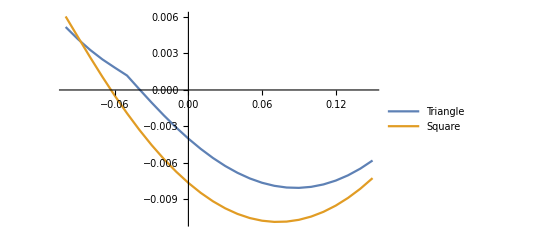

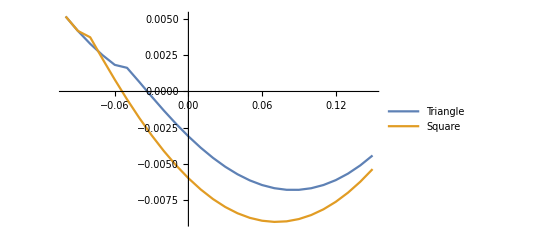

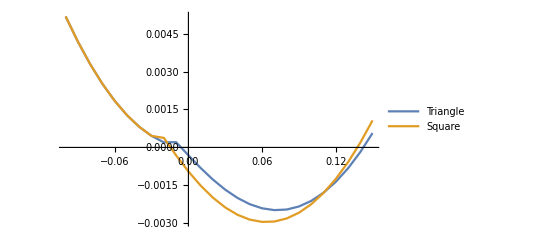

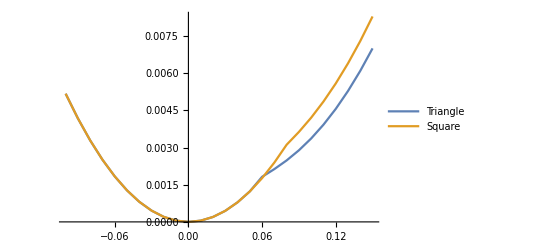

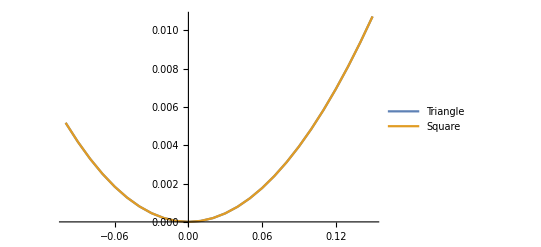

-Graphics-

```mathematica
n=Table[x,{x,-0.1,0.15,0.01}];
ListLinePlot[{Transpose[{n,Subscript[D, t][[1]]}],Transpose[{n,Subscript[D, s][[1]]}]},PlotLegends->{"Triangle","Square"}]
ListLinePlot[{Transpose[{n,Subscript[D, t][[5]]}],Transpose[{n,Subscript[D, s][[5]]}]},PlotLegends->{"Triangle","Square"}]
ListLinePlot[{Transpose[{n,Subscript[D, t][[10]]}],Transpose[{n,Subscript[D, s][[10]]}]},PlotLegends->{"Triangle","Square"}]
ListLinePlot[{Transpose[{n,Subscript[D, t][[15]]}],Transpose[{n,Subscript[D, s][[15]]}]},PlotLegends->{"Triangle","Square"}]
ListLinePlot[{Transpose[{n,Subscript[D, t][[20]]}],Transpose[{n,Subscript[D, s][[20]]}]},PlotLegends->{"Triangle","Square"}]
```